```mathematica
Clear[f];
Vfene[r_, ϵ_, r0_, Δ_] := - (ϵ/2) Log[1 - ((r -r0)/Δ)^2];
Vmorse[x_, ϵ_, x0_, a_] := ϵ (1-Exp[ - a ( x - x0)])^2;
Vharm[r_, k_, r0_] := (k / 2) (r - r0)^2;
Vlj[r_, ϵ_, σ_] := 4 ϵ ( (σ/r)^12 - (σ/r)^6);
Vmod[θ_,a_,θ0_] := 1 - a(θ-θ0)^2;
Vsmooth[x_, b_, xc_] := b ( x-xc)^2
```

```mathematica
Vmorse[r,ϵ,r0,a]
```

(1-ⅇ^(-a (r-r0)))^2 ϵ

```mathematica
D[Vmorse[r,ϵ,r0,a],r]
```

2 a ⅇ^(-a (r-r0)) (1-ⅇ^(-a (r-r0))) ϵ

```mathematica
dVmdr[r_,ϵ_,r0_,a_] := Evaluate[D[Vmorse[r,ϵ,r0,a],r]]
dVmdr[rlow,ϵ,r0,a]
```

2 a ⅇ^(-a (-r0+rlow)) (1-ⅇ^(-a (-r0+rlow))) ϵ

```mathematica
dVsdr[x_,b_,xc_] := Evaluate[D[Vsmooth[x,b,xc],x]]
```

```mathematica
2 b (x-xc)
```

```mathematica
Subscript[ϵ, 1]=1.077; Subscript[a, 1]=8; Subscript[r0, 1]=0.4; Subscript[rc, 1]=0.75;  Subscript[rhigh, 1]=0.70; Subscript[rlow, 1]=0.34;
Solve[ {Vmorse[Subscript[rlow, 1],Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]]- Vmorse[Subscript[rc, 1],Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]]== Subscript[ϵ, 1] Vsmooth[Subscript[rlow, 1],b, xc],2 Subscript[a, 1] Subscript[ϵ, 1] ⅇ^(-Subscript[a, 1] (Subscript[rlow, 1]-Subscript[r0, 1])) (1-ⅇ^(-Subscript[a, 1](Subscript[rlow, 1]-Subscript[r0, 1]))) Subscript[ϵ, 1] == 2 b (Subscript[rlow, 1]-xc) Subscript[ϵ, 1]},{b,xc}, Reals]
```

{{b→-2.68106×10^16,xc→0.34},{b→-51.6985,xc→0.281418}}

```mathematica
Vmorse[Subscript[rlow, 1],Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]]
```

0.408773

```mathematica
Vsmooth[Subscript[rlow, 1], b, xc]
```

```mathematica
b (0.34-xc)^2
```

```mathematica
dVmdr[Subscript[rlow, 1],Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]]
```

-17.1566

```mathematica
Vrc = Vmorse[Subscript[rc, 1],Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]];
```

```mathematica
myVar=FindRoot[ {Evaluate[Vmorse[Subscript[rlow, 1],Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]]]- Vrc== Subscript[ϵ, 1] Vsmooth[Subscript[rlow, 1],b, xc], 
dVmdr[Subscript[rlow, 1],Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]] == Subscript[ϵ, 1] dVsdr[Subscript[rlow, 1],b,xc]}, {{b,-50}, {xc, Subscript[rlow, 1]-0.1}}, MaxIterations-> 10000];
```

```mathematica
Subscript[b, 1low]=b/.myVar; Subscript[xc, 1low]= xc/.myVar;
Subscript[b, 1low]
Subscript[xc, 1low]
```

-126.243

0.276908

```mathematica
myVar=FindRoot[ {Evaluate[Vmorse[Subscript[rhigh, 1],Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]]]- Vrc== Subscript[ϵ, 1] Vsmooth[Subscript[rhigh, 1],b, xc], 
dVmdr[Subscript[rhigh, 1],Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]] == Subscript[ϵ, 1] dVsdr[Subscript[rhigh, 1],b,xc]},{{b,10},{xc,Subscript[rhigh, 1]+0.1}}, MaxIterations-> 10000];
Subscript[b, 1high]=b/.myVar; Subscript[xc, 1high]= xc/.myVar;

Subscript[b, 1high]
```

-7.87708

```mathematica
Subscript[xc, 1high]
```

0.783775

```mathematica
Plot [{ Vmorse[x,Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]] - Vrc, Subscript[ϵ, 1] Vsmooth[x, Subscript[b, 1low], Subscript[xc, 1low]], Subscript[ϵ, 1] Vsmooth[x, Subscript[b, 1high],Subscript[xc, 1high]]}, {x, 0, 1.5}, PlotRange-> {{0,1},{-1,1}}];
```

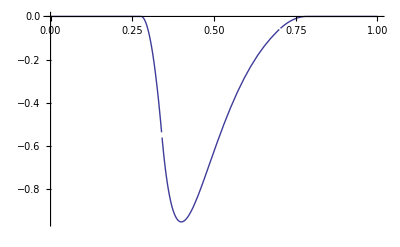

```mathematica
f1[r_] :=   Piecewise[{
{0 ,r <Subscript[xc, 1low] },
{Subscript[ϵ, 1] Vsmooth[r,Subscript[b, 1low],Subscript[xc, 1low]],Subscript[xc, 1low]<r && r < Subscript[rlow, 1]}, {Vmorse[r,Subscript[ϵ, 1],Subscript[r0, 1],Subscript[a, 1]] - Vrc , Subscript[rlow, 1]<r && r < Subscript[rhigh, 1]}, {Subscript[ϵ, 1] Vsmooth[r, Subscript[b, 1high],Subscript[xc, 1high]],r > Subscript[rhigh, 1]&& r<Subscript[xc, 1high]},
{0, r> Subscript[xc, 1high]} 
}]
Plot[f1[r], {r, 0, 1}]
```